0.700357

Part::partw: Part {1,2} of x[t] does not exist.

{{x→InterpolatingFunction[{{0., 1.33947}}, <>]}}

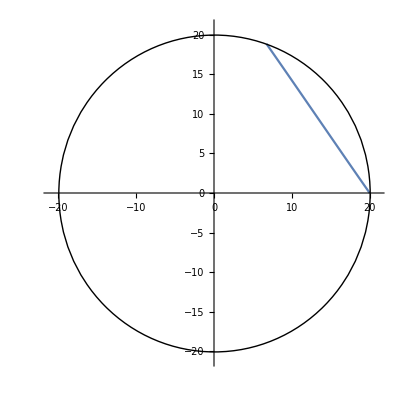

```mathematica
Clear[t]
r=20; (*m, radius of cylinder*)
a = 9.81; (*m/s^2, radial acceleration at edge of cylinder*)
ω = Sqrt[a/r]; (*rad/s* angular velocity of cylinder*)
ω
(*Clear[ω,r]*)
θ = ω*t;
RtoS[t_] := { (*change of basis from Rotating to Fixed (standard) reference frame*)
{-Sin[ω*t],-Cos[ω*t],r*Cos[ω*t]},
{Cos[ω*t],-Sin[ω*t],r*Sin[ω*t]},
{0,0,1}
};

StoR[t_]:=Simplify[Inverse[RtoS[t]]]; (*change of basis matrix from Fixed to Rotating reference frame*)
posRot = {0,0,1}; (*initial position in rotating refernce frame*)
vRot = {0,10,0}; (*initial velocity in rotating reference frame*)


vAir[{x_,y_,q_}]:={-y,x,0}; (*velocity of air in absolute coordinates*)
Cd = 0.3; (*drag coeficient*)
ρ=1.2; (*kg/m^3, density of air*)
A = 0.004; (*m^2, cross sectional area of ball*)
m = 0.145; (*kg* mass of ball*)
ballAirV[p_,v_] := vAir[p]-v; (*airspeed of ball as function of position and absolute velocity*)
dragForce[p_,v_]:=.5*Cd*A*ρ*Norm[ballAirV[p,v]]^2 *ballAirV[p,v]/Norm[ballAirV[p,v]]  (*drag force on ball as function of position and absolute velocity*)
Clear[s] 
s=NDSolve[
{
m*x''[t]==dragForce[x[t],x'[t]],(*single differential equation*)
x[0]==RtoS[0].posRot,                               (*initial position in fixed frame*)
x'[0]==RtoS'[0].posRot+RtoS[0].vRot,(*initial velocity in fixed frame*)
WhenEvent[Norm[x[t][[{1,2}]]]>=r,end=t;"StopIntegration"] (*stop when the ball hits the edge of the cylinder, save the last time in end*)
},x,{t,0,Infinity}
]
ParametricPlot[Evaluate[x[t]/.s][[1,{1,2}]],{t,0,end},Epilog->{Black,Circle[{0,0},20]},PlotRange->{{-r-1,r+1},{-r-1,r+1}}]
```